```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g- t- t (1-loop)

generic model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC} initialized

classes model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA} initialized

in total: 1 Particles insertion

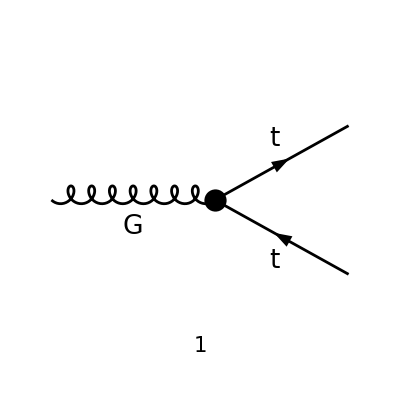

```mathematica
tops0 = CreateTopologies[0,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[tops0,processGGT, InsertionLevel-> {Particles},GenericModel->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC" ,ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9],V[4]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{k1},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 1 Particles amplitude

-ⅈ gs T_Col2Col3^Glu1 (π^2 itri yDM^2 (γ^Lor1.(γ̄)^6 (2 C00ren-(C1+C11+C12) (k1·p1+k1·p2-p1^2-p2^2)+k1^2 (C1+2 C12))-(C1+C11+C12) ((k1^Lor1-2 p1^Lor1) (γ·p1).(γ̄)^6+(k1^Lor1-2 p2^Lor1) (γ·p2).(γ̄)^6)+(γ·k1).(γ̄)^6 ((C1+2 C11) k1^Lor1-(C1+C11+C12) (p1^Lor1+p2^Lor1))+2 deltaCTL γ^Lor1.(γ̄)^7)+γ^Lor1.((γ̄)^6+(γ̄)^7))

```mathematica
(* Fix Gauge and replace C00ren by the PV loop integrals and the counter-term *)
ampC =ampB/.{LorentzIndex[a_,D]->LorentzIndex[μ,D],GaugeXi[V[Index[Generic,5]]]->1};
```

```mathematica
(* Remove SM contribution *)
ampSM=gs SeriesCoefficient[ampC,{gs,0,1},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

```mathematica
ampEsimp=FCReplaceMomenta[ampC,{k1->p1+p2}];
```

```mathematica
moms=Cases2[ampEsimp,DiracGamma]
```

{(γ̄)^6,(γ̄)^7,γ^μ,γ·p1,γ·p2}

```mathematica
ampEsimp2=FullSimplify[ExpandScalarProduct[DiracSimplify[ampEsimp/.{DiracGamma[7]->1-DiracGamma[6]}]]]
```

-ⅈ π^2 gs itri yDM^2 T_Col2Col3^Glu1 (γ^μ.(γ̄)^6 (2 (C00ren+(C12-C11) (p1·p2)-deltaCTL)+p1^2 (C1+2 C12)+p2^2 (C1+2 C12))+(γ·p2).(γ̄)^6 ((C1+2 C11) p2^μ-(C1+2 C12) p1^μ)+(γ·p1).(γ̄)^6 ((C1+2 C11) p1^μ-(C1+2 C12) p2^μ)+2 deltaCTL γ^μ)

```mathematica
spinorChains=Tally[Cases[{ampEsimp2},DiracGamma[___].DiracGamma[___],All]][[All,1]]
singleGammas=Cases2[ampEsimp2,DiracGamma]
allTerms=Sort[Join[spinorChains,singleGammas]];
```

{(γ·p2).(γ̄)^6,(γ·p1).(γ̄)^6,γ^μ.(γ̄)^6}

{(γ̄)^6,γ^μ,γ·p1,γ·p2}

### Coefficients for each term

```mathematica
Table[{allTerms[[i]],FullSimplify[Coefficient[ampEsimp2,allTerms[[i]]]]},{i,1,Length[allTerms]}]
```

((γ̄)^6 | 0
γ^μ | -2 ⅈ π^2 deltaCTL gs itri yDM^2 T_Col2Col3^Glu1
γ·p1 | 0
γ·p2 | 0
γ^μ.(γ̄)^6 | -ⅈ π^2 gs itri yDM^2 T_Col2Col3^Glu1 (2 (C00ren+(C12-C11) (p1·p2)-deltaCTL)+p1^2 (C1+2 C12)+p2^2 (C1+2 C12))
(γ·p1).(γ̄)^6 | -ⅈ π^2 gs itri yDM^2 T_Col2Col3^Glu1 ((C1+2 C11) p1^μ-(C1+2 C12) p2^μ)
(γ·p2).(γ̄)^6 | -ⅈ π^2 gs itri yDM^2 T_Col2Col3^Glu1 ((C1+2 C11) p2^μ-(C1+2 C12) p1^μ))

```mathematica
Simplify[Coefficient[ampEsimp2,C00ren]]
```

-2 ⅈ π^2 gs itri yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1

```mathematica
Simplify[Coefficient[ampEsimp2,C1]]
```

-ⅈ π^2 gs itri yDM^2 T_Col2Col3^Glu1 ((p1^2+p2^2) γ^μ.(γ̄)^6+(p1^μ-p2^μ) (γ·p1).(γ̄)^6+(p2^μ-p1^μ) (γ·p2).(γ̄)^6)

```mathematica
Simplify[Coefficient[ampEsimp2,C11]]
```

-2 ⅈ π^2 gs itri yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p1).(γ̄)^6-γ^μ.(γ̄)^6 (p1·p2)+p2^μ (γ·p2).(γ̄)^6)

```mathematica
Simplify[Coefficient[ampEsimp2,C12]]
```

2 ⅈ π^2 gs itri yDM^2 T_Col2Col3^Glu1 (-γ^μ.(γ̄)^6 (p1·p2+p1^2+p2^2)+p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)